```mathematica
k1 = 5;
k2 = 1;
T2 = 15;
k3 = 20;
T3 = 10;
W = k1*(k2/(T2*p+1))*(k3/(T3*p+1));
F = Simplify[W/(1+W)]
```

100/(101+25 p+150 p^2)

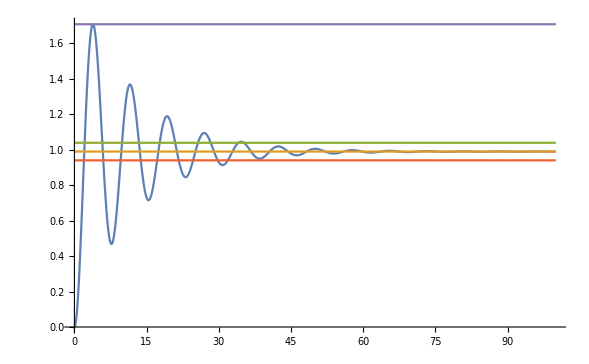

72.5638

{t→35.2047}

```mathematica
K = 100;

result = DSolveValue[{(K+1)y[t]+25y'[t]+150y''[t]==K*HeavisideTheta[t],y[0]==0,y'[0]==0},y[t],t];

hSenter = K/(K+1);
hMax = FindMaximum[result,{t,0,100}];

Plot[{result,hSenter,hSenter+0.05*hSenter,hSenter-0.05*hSenter,hMax},{t,0,100},PlotRange->All]
sigma = (FindMaxValue[result,{t,0,100}]-hSenter)/hSenter*100
FindRoot[result ==hSenter+0.05*hSenter,{t,35}]
```

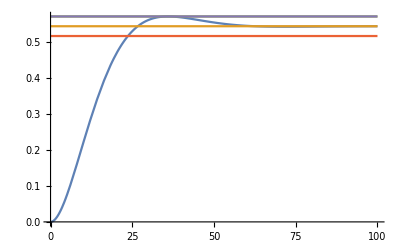

5.

{t→35.9488}

```mathematica
(*-------------------------------5----------------------------------*)
K = 1.1872389;

result = DSolveValue[{(K+1)y[t]+25y'[t]+150y''[t]==K*HeavisideTheta[t],y[0]==0,y'[0]==0},y[t],t];

hSenter = K/(K+1);
hMax = FindMaximum[result,{t,0,100}];

Plot[{result,hSenter,hSenter+0.05*hSenter,hSenter-0.05*hSenter,hMax},{t,0,100},PlotRange->All]
sigma = (FindMaxValue[result,{t,0,100}]-hSenter)/hSenter*100
FindRoot[result ==hSenter+0.05*hSenter,{t,30}]
```

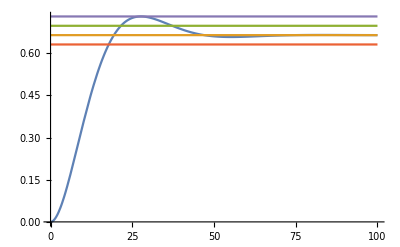

10.

{t→37.2228}

```mathematica
(*-------------------------------10----------------------------------*)
K = 1.98076;

result = DSolveValue[{(K+1)y[t]+25y'[t]+150y''[t]==K*HeavisideTheta[t],y[0]==0,y'[0]==0},y[t],t];

hSenter = K/(K+1);
hMax = FindMaximum[result,{t,0,100}];

Plot[{result,hSenter,hSenter+0.05*hSenter,hSenter-0.05*hSenter,hMax},{t,0,100},PlotRange->All]
sigma = (FindMaxValue[result,{t,0,100}]-hSenter)/hSenter*100
FindRoot[result ==hSenter+0.05*hSenter,{t,30}]
```

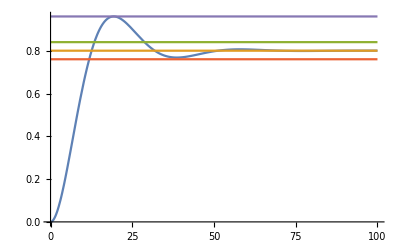

20.

{t→28.7445}

```mathematica
(*-------------------------------20----------------------------------*)
K = 4.01066;

result = DSolveValue[{(K+1)y[t]+25y'[t]+150y''[t]==K*HeavisideTheta[t],y[0]==0,y'[0]==0},y[t],t];

hSenter = K/(K+1);
hMax = FindMaximum[result,{t,0,100}];

Plot[{result,hSenter,hSenter+0.05*hSenter,hSenter-0.05*hSenter,hMax},{t,0,100},PlotRange->All]
sigma = (FindMaxValue[result,{t,0,100}]-hSenter)/hSenter*100
FindRoot[result ==hSenter+0.05*hSenter,{t,35}]
```

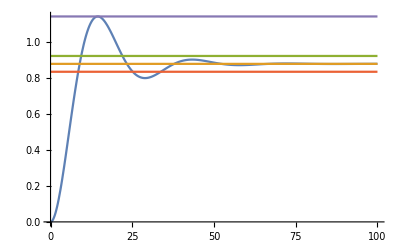

30.

{t→33.7205}

```mathematica
(*-------------------------------30----------------------------------*)
K = 7.1341;

result = DSolveValue[{(K+1)y[t]+25y'[t]+150y''[t]==K*HeavisideTheta[t],y[0]==0,y'[0]==0},y[t],t];

hSenter = K/(K+1);
hMax = FindMaximum[result,{t,0,100}];

Plot[{result,hSenter,hSenter+0.05*hSenter,hSenter-0.05*hSenter,hMax},{t,0,100},PlotRange->All]
sigma = (FindMaxValue[result,{t,0,100}]-hSenter)/hSenter*100
FindRoot[result ==hSenter-0.05*hSenter,{t,33}]
```

```mathematica
(*---------------------Часть 2-------------------------*)
```

```mathematica
k1 = 0.1;
k2= 6;
k3 = 0.5;
T3 = 20;
k4 = 5;
T4 = 5;
v = 2;
a = 9.8;
W1 = k1;
W2 = k2/s;
W3 = k3/(T3*s+1);
W4 = k4/(T4*s+1);
W = FullSimplify[(W1+W2)*W3*W4];
Fe = Simplify[1/(1+W)];
Print["Функція за помилкою ",Fe]
(*------------------------------*)
resultX1 = LaplaceTransform[HeavisideTheta[t],t,s];
(*------------------------------*)
resultX2 = LaplaceTransform[v*t,t,s];
(*------------------------------*)
resultX3 = LaplaceTransform[a*t^2,t,s];
(*------------------------------------------*)
```

Функція за помилкою 1/(1+(0.25+15./s)/(1+25 s+100 s^2))

0

0.0666667

Indeterminate

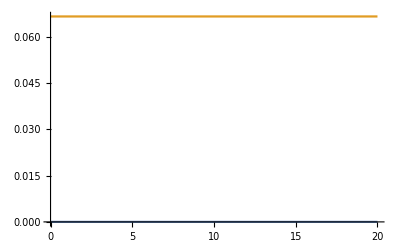

```mathematica
(*------------------------------*)
eps1 = Limit[s*Fe*resultX1,s->0]
eps2 = Limit[s*Fe*resultX2,s->0]
eps3 = Limit[s*Fe*resultX3,s->0]
Plot[{eps1,eps2, eps3},{t,0,20}]
```